# Fits to Brody distribution, and calculations for density of states

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
bins=Table[x,{x,0,5,0.2}];
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
Ewindowsize=15.0;
```

## Run0

```mathematica
rundata0=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			80

LobattoPoints		NumChannels	Order
80			80		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
20.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff0-Ewindowsize<#<Ecutoff0-1.&;
curvestemp0=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/AdiabaticCurves.dat"]];
Curves0=Table[Table[{curvestemp0[[1,i]],curvestemp0[[j,i]]},{i,1,Length[curvestemp0[[1]]]}],{j,2,Length[curvestemp0]}];
Evals0=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/Eigenvals.dat"]];
Ecutoff0=Evals0[[4]]
Evals0=Sort[Drop[Evals0,1;;4]];
eValsBound0 = Sort[Select[Evals0,SampleRange]]
```

-44.5095

{-58.9159,-58.1359,-57.8453,-57.6367,-57.4647,-57.0817,-56.9889,-56.8279,-56.5663,-56.4086,-56.1083,-55.9379,-55.7941,-55.6924,-55.4071,-55.358,-55.0319,-54.1721,-54.0766,-53.861,-53.5784,-53.229,-53.1496,-53.0108,-52.8458,-52.7331,-52.5844,-52.4082,-52.2474,-51.9512,-51.7618,-51.6723,-51.5602,-51.5081,-51.3234,-51.1416,-50.8119,-50.6767,-50.4689,-50.3717,-50.162,-49.9728,-49.8434,-49.6687,-49.5996,-49.4682,-49.322,-49.1247,-48.8864,-48.8203,-48.5751,-48.4666,-48.3016,-48.114,-48.0605,-47.9749,-47.8144,-47.6364,-47.4633,-47.4427,-47.3457,-47.2917,-47.1616,-47.0736,-46.9488,-46.8558,-46.6191,-46.469,-46.4361,-46.3375,-46.2006,-46.1038,-45.9457,-45.9145,-45.7217,-45.5649}

```mathematica
Length[eValsBound0]
```

76

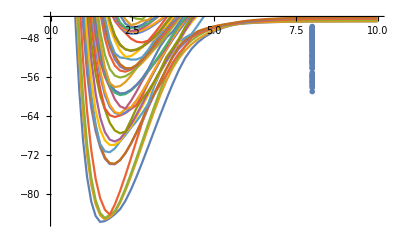

```mathematica
pcurves0=ListPlot[Curves0,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp0[[2]]],Ecutoff0+1}];
penergies0=ListPlot[Table[{8,eValsBound0[[i]]},{i,1,Length[eValsBound0]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves0,penergies0]
```

```mathematica
Es0=Table[eValsBound0[[i+1]]-eValsBound0[[i]],{i,1,Length[eValsBound0]-1}];
eTrim0= Select[Es0,#>0.0000001&];
avg0 = Mean[eTrim0];
eTrim0 = eTrim0/avg0;
(*Sort[eTrim1];*)
Length[Es0];
Length[eTrim0];
ρ0=1/avg0;
EspaceBin0=BinCounts[eTrim0,{bins}];
NormBrodyBinCs0=Table[EspaceBin0[[i]]/Total[EspaceBin0]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist0 = Table[{bFit[[i]],NormBrodyBinCs0[[i]]},{i,1,Length[bFit]}]
phist0=ListPlot[brodyPdist0,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars0 = FindFit[brodyPdist0,{PBrody[s,w],w>0,w<1},{w},s]
pfit0=Plot[PBrody[s,w/.pars0],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.2},{0.3,0.4},{0.5,0.8},{0.7,0.666667},{0.9,1.13333},{1.1,0.733333},{1.3,0.266667},{1.5,0.133333},{1.7,0.266667},{1.9,0.2},{2.1,0.0666667},{2.3,0.},{2.5,0.},{2.7,0.},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.0666667},{4.5,0.},{4.7,0.},{4.9,0.0666667}}

{w→0.999995}

```mathematica
ρ0
```

5.61755

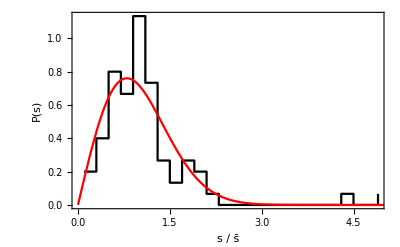

```mathematica
Show[phist0,pfit0,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run1

```mathematica
rundata1=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run1/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			80

LobattoPoints		NumChannels	Order
80			80		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
20.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.d0		1.d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff1-Ewindowsize<#<Ecutoff1-1.&;
curvestemp1=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run1/AdiabaticCurves.dat"]];
Curves1=Table[Table[{curvestemp1[[1,i]],curvestemp1[[j,i]]},{i,1,Length[curvestemp1[[1]]]}],{j,2,Length[curvestemp1]}];
Evals1=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run1/Eigenvals.dat"]];
Ecutoff1=Evals1[[4]]
Evals1=Sort[Drop[Evals1,1;;4]];
eValsBound1 = Sort[Select[Evals1,SampleRange]]
```

-43.2396

{-57.7493,-57.3873,-57.0259,-55.7625,-54.4411,-53.9038,-53.3546,-53.0457,-52.3153,-52.3019,-50.8846,-50.4443,-49.6802,-49.3114,-49.0257,-48.9467,-48.2993,-47.9963,-47.6593,-47.2629,-47.1275,-46.5716,-45.8461,-45.8097,-45.5161,-45.2855,-45.0039,-44.5644}

```mathematica
Length[eValsBound1]
```

28

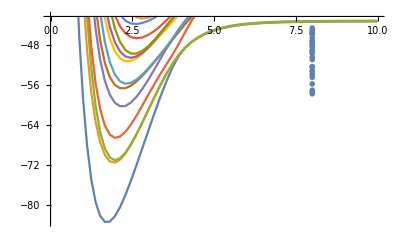

```mathematica
pcurves1=ListPlot[Curves1,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp1[[2]]],Ecutoff1+1}];
penergies1=ListPlot[Table[{8,eValsBound1[[i]]},{i,1,Length[eValsBound1]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves1,penergies1]
```

```mathematica
Es1=Table[eValsBound1[[i+1]]-eValsBound1[[i]],{i,1,Length[eValsBound1]-1}];
eTrim1= Select[Es1,#>0.0000001&];
avg1 = Mean[eTrim1];
eTrim1 = eTrim1/avg1;
(*Sort[eTrim1];*)
Length[Es1];
Length[eTrim1];
ρ1=1/avg1;
EspaceBin1=BinCounts[eTrim1,{bins}];
NormBrodyBinCs1=Table[EspaceBin1[[i]]/Total[EspaceBin1]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist1 = Table[{bFit[[i]],NormBrodyBinCs1[[i]]},{i,1,Length[bFit]}]
phist1=ListPlot[brodyPdist1,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars1 = FindFit[brodyPdist1,{PBrody[s,w],w>0,w<1},{w},s]
pfit1=Plot[PBrody[s,w/.pars1],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.555556},{0.3,0.185185},{0.5,0.555556},{0.7,1.2963},{0.9,0.555556},{1.1,0.555556},{1.3,0.185185},{1.5,0.555556},{1.7,0.},{1.9,0.},{2.1,0.},{2.3,0.},{2.5,0.185185},{2.7,0.185185},{2.9,0.185185},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.703815}

```mathematica
ρ1
```

2.04779

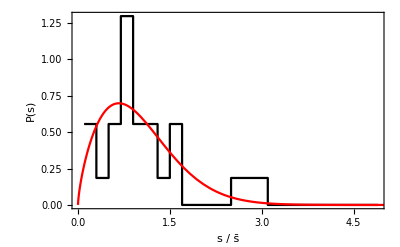

```mathematica
Show[phist1,pfit1,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run2

```mathematica
rundata2=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run2/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
40			80

LobattoPoints		NumChannels	Order
80			80		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
20.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.d0		1.d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.25d0		0d0 		0.5d0

Left		Right		Bot		Top
0		1		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff2-Ewindowsize<#<Ecutoff2-1&
curvestemp2=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run2/AdiabaticCurves.dat"]];
Curves2=Table[Table[{curvestemp2[[1,i]],curvestemp2[[j,i]]},{i,1,Length[curvestemp2[[1]]]}],{j,2,Length[curvestemp2]}];
Evals2=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run2/Eigenvals.dat"]];
Ecutoff2=Evals2[[4]]
Evals2=Sort[Drop[Evals2,1;;4]];
eValsBound2 = Sort[Select[Evals2,SampleRange]]
```

Ecutoff2-Ewindowsize<#1<Ecutoff2-1&

-43.2396

{-58.0912,-58.0264,-57.1808,-56.8717,-56.484,-55.8068,-55.2755,-54.9594,-54.0116,-53.3361,-53.1137,-52.2306,-51.7618,-51.5777,-50.9177,-50.6876,-50.5613,-50.3588,-49.6189,-49.0882,-49.0741,-48.7044,-48.6857,-47.8724,-47.5591,-47.1458,-46.9001,-46.5436,-46.5007,-46.3773,-45.5815,-45.4982,-45.1164,-45.0653,-44.9741,-44.8257,-44.6645,-44.3491}

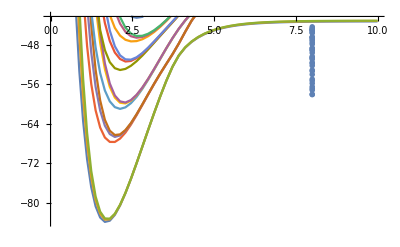

```mathematica
pcurves2=ListPlot[Curves2,PlotMarkers->None,Joined->True,PlotRange->{Min[curvestemp2[[2]]],Ecutoff2+1}];
penergies2=ListPlot[Table[{8,eValsBound2[[i]]},{i,1,Length[eValsBound2]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves2,penergies2]
```

```mathematica
Es2=Table[eValsBound2[[i+1]]-eValsBound2[[i]],{i,1,Length[eValsBound2]-1}];
eTrim2 = Select[Es2,#>0.0000001&];
avg2 = Mean[eTrim2];
eTrim2 = eTrim2/avg2;
(*Sort[eTrim2];*)
Length[Es2];
Length[eTrim2];
ρ2=1/avg2;
EspaceBin2=BinCounts[eTrim2,{bins}];
NormBrodyBinCs2=Table[EspaceBin2[[i]]/Total[EspaceBin2]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist2 = Table[{bFit[[i]],NormBrodyBinCs2[[i]]},{i,1,Length[bFit]}]
phist2=ListPlot[brodyPdist2,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars2 = FindFit[brodyPdist2,{PBrody[s,w],w>0,w<1},{w},s]
pfit2=Plot[PBrody[s,w/.pars2],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.675676},{0.3,0.675676},{0.5,0.540541},{0.7,0.27027},{0.9,0.810811},{1.1,0.405405},{1.3,0.135135},{1.5,0.27027},{1.7,0.135135},{1.9,0.405405},{2.1,0.27027},{2.3,0.27027},{2.5,0.135135},{2.7,0.},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.186142}

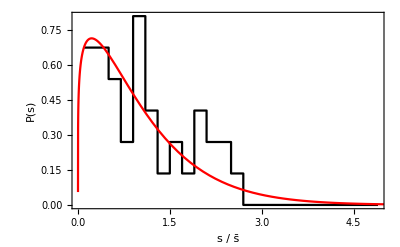

```mathematica
Show[phist2,pfit2,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

## Run3

```mathematica
rundata3=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run3/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
80			80

LobattoPoints		NumChannels	Order
80			120		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
20.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.d0		1.d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff3-Ewindowsize<#<Ecutoff3-1&
curvestemp3=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run3/AdiabaticCurves.dat"]];
Curves3=Table[Table[{curvestemp3[[1,i]],curvestemp3[[j,i]]},{i,1,Length[curvestemp3[[1]]]}],{j,2,Length[curvestemp3]}];
Evals3=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run3/Eigenvals.dat"]];
Ecutoff3=Evals3[[4]]
Evals3=Sort[Drop[Evals3,1;;4]];
eValsBound3 = Sort[Select[Evals3,SampleRange]]
```

Ecutoff3-Ewindowsize<#1<Ecutoff3-1&

-43.2396

{-58.0911,-58.0264,-57.7493,-57.3873,-57.1808,-57.0259,-56.8717,-56.484,-55.8068,-55.7625,-55.2755,-54.9594,-54.4411,-54.0116,-53.9038,-53.3546,-53.3361,-53.1137,-53.0457,-52.3153,-52.3019,-52.2306,-51.7618,-51.5777,-50.9177,-50.8846,-50.6876,-50.5612,-50.4442,-50.3588,-49.6802,-49.6189,-49.3113,-49.0882,-49.0741,-49.0257,-48.9467,-48.7044,-48.6857,-48.2993,-47.9963,-47.8724,-47.6593,-47.5591,-47.2629,-47.1458,-47.1275,-46.9001,-46.5716,-46.5436,-46.5007,-46.3773,-45.8461,-45.8096,-45.5815,-45.5161,-45.4982,-45.2854,-45.1164,-45.0653,-45.0038,-44.9741,-44.8257,-44.6645,-44.5644,-44.3491}

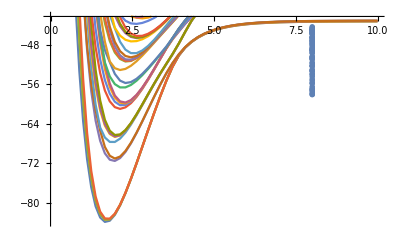

```mathematica
pcurves3=ListPlot[Curves3,Joined->True,PlotRange->{Min[curvestemp3[[2]]],Ecutoff3+1}];
penergies3=ListPlot[Table[{8,eValsBound3[[i]]},{i,1,Length[eValsBound3]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves3,penergies3]
```

```mathematica
Es3=Table[eValsBound3[[i+1]]-eValsBound3[[i]],{i,1,Length[eValsBound3]-1}];
eTrim3 = Select[Es3,#>0.0000001&];
avg3 = Mean[eTrim3];
eTrim3 = eTrim3/avg3;
Sort[eTrim3];
Length[Es3];
Length[eTrim3];
ρ3=1/avg3;
EspaceBin3=BinCounts[eTrim3,{bins}];
NormBrodyBinCs3=Table[EspaceBin3[[i]]/Total[EspaceBin3]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist3 = Table[{bFit[[i]],NormBrodyBinCs3[[i]]},{i,1,Length[bFit]}]
phist3=ListPlot[brodyPdist3,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Blue}];
pars3 = FindFit[brodyPdist3,{PBrody[s,w],w>0,w<1},{w},s]
pfit3=Plot[PBrody[s,w/.pars3],{s,0,5},PlotRange->All,PlotStyle->{Green}];
```

{{0.1,0.769231},{0.3,0.846154},{0.5,0.692308},{0.7,0.384615},{0.9,0.230769},{1.1,0.615385},{1.3,0.0769231},{1.5,0.384615},{1.7,0.0769231},{1.9,0.153846},{2.1,0.0769231},{2.3,0.153846},{2.5,0.230769},{2.7,0.},{2.9,0.},{3.1,0.0769231},{3.3,0.153846},{3.5,0.0769231},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.0551976}

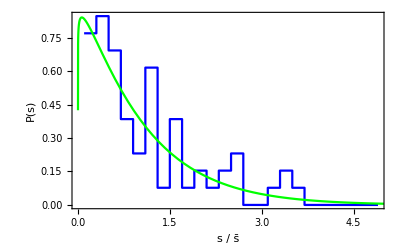

```mathematica
pall3=Show[phist3,pfit3,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

##### Analysis so far

Runs 1 and 2 have taken advantage of a possible symmetry by further reducing the coordinate space.  If my guess is right, then the density of states for run3 should be roughly twice that of run 1 and 2 since I expect both “even and odd” states about phi = π/4 to be present in run 3, but only even states in run1 and odd states in run2

```mathematica
ρ1
ρ2
ρ3
```

2.04779

2.69246

4.72999

```mathematica
ρ1+ρ2
```

4.74025

Further, I expect that if these states (even and odd) do not couple since the Hamiltonian is symmetric about ϕ=π/4, then overlaying these two distributions will result in a distribution similar to that of run3

```mathematica
eValsBoundCombined =Sort[ Flatten[{eValsBound1,eValsBound2}]]
EsCombined=Table[eValsBoundCombined[[i+1]]-eValsBoundCombined[[i]],{i,1,Length[eValsBoundCombined]-1}];
eTrimCombined = Select[EsCombined,#>0.0000001&];
avgCombined = Mean[eTrimCombined];
eTrimCombined = eTrimCombined/avgCombined;
(*Sort[eTrimCombined];*)
Length[eTrimCombined];
ρCombined=1/avgCombined;
EspaceBinCombined=BinCounts[eTrimCombined,{bins}];
NormBrodyBinCsCombined=Table[EspaceBinCombined[[i]]/Total[EspaceBinCombined]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdistCombined = Table[{bFit[[i]],NormBrodyBinCsCombined[[i]]},{i,1,Length[bFit]}]
phistCombined=ListPlot[brodyPdistCombined,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->{Black,Dashed}];
parsCombined = FindFit[brodyPdistCombined,{PBrody[s,w],w>0,w<1},{w},s]
pfitCombined=Plot[PBrody[s,w/.parsCombined],{s,0,5},PlotRange->All,PlotStyle->{Red,Dashed}];
```

{-58.0912,-58.0264,-57.7493,-57.3873,-57.1808,-57.0259,-56.8717,-56.484,-55.8068,-55.7625,-55.2755,-54.9594,-54.4411,-54.0116,-53.9038,-53.3546,-53.3361,-53.1137,-53.0457,-52.3153,-52.3019,-52.2306,-51.7618,-51.5777,-50.9177,-50.8846,-50.6876,-50.5613,-50.4443,-50.3588,-49.6802,-49.6189,-49.3114,-49.0882,-49.0741,-49.0257,-48.9467,-48.7044,-48.6857,-48.2993,-47.9963,-47.8724,-47.6593,-47.5591,-47.2629,-47.1458,-47.1275,-46.9001,-46.5716,-46.5436,-46.5007,-46.3773,-45.8461,-45.8097,-45.5815,-45.5161,-45.4982,-45.2855,-45.1164,-45.0653,-45.0039,-44.9741,-44.8257,-44.6645,-44.5644,-44.3491}

{{0.1,0.769231},{0.3,0.846154},{0.5,0.692308},{0.7,0.384615},{0.9,0.230769},{1.1,0.615385},{1.3,0.0769231},{1.5,0.384615},{1.7,0.0769231},{1.9,0.153846},{2.1,0.0769231},{2.3,0.153846},{2.5,0.230769},{2.7,0.},{2.9,0.},{3.1,0.0769231},{3.3,0.153846},{3.5,0.0769231},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

{w→0.0551976}

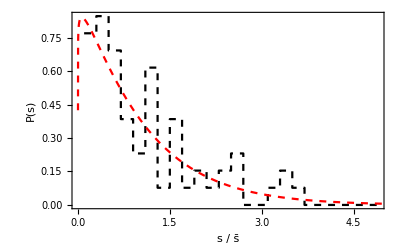

```mathematica
pcomb=Show[phistCombined,pfitCombined,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

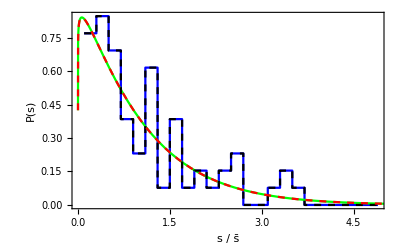

```mathematica
Show[pall3,pcomb]
```

## Run4

```mathematica
rundata4=Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run4/4BodySVD.par","text"]
```

xPoints (phi)		yPoints (theta)
80			80

LobattoPoints		NumChannels	Order
80			120		7

PotentialDepth		Rmin		Rmax		alpha (turns V on and off)
20.d0			0d0		10.d0		1.d0

m1		m2		m3		m4
1.d0		1.d0		1.5d0		1.5d0

xMin		xMax		yMin		yMax   (enter in units of pi)
0d0		0.5d0		0d0 		0.5d0

Left		Right		Bot		Top
0		0		2		1



!  At top -- Phi(theta=pi/2,phi)=0 for odd parity so choose Top = 0
      	     Phi'(theta=pi/2,phi)=0 for even parity so choose Top = 1

```mathematica
SampleRange=Ecutoff4-Ewindowsize<#<Ecutoff4-1&
curvestemp4=Transpose[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run4/AdiabaticCurves.dat"]];
Curves4=Table[Table[{curvestemp4[[1,i]],curvestemp4[[j,i]]},{i,1,Length[curvestemp4[[1]]]}],{j,2,Length[curvestemp4]}];
Evals4=Flatten[Import["/Users/niravmehta/Documents/GitHub/4BodySVD/runs20/run4/Eigenvals.dat"]];
Ecutoff4=Evals4[[4]]
Evals4=Sort[Drop[Evals4,1;;4]];
eValsBound4 = Sort[Select[Evals4,SampleRange]]
```

Ecutoff4-Ewindowsize<#1<Ecutoff4-1&

-44.5098

{-58.9159,-58.1359,-57.8453,-57.6367,-57.4648,-57.0818,-56.989,-56.828,-56.5663,-56.4086,-56.1083,-55.9379,-55.7942,-55.6924,-55.4072,-55.358,-55.0319,-54.1721,-54.0767,-53.8611,-53.5785,-53.2291,-53.1498,-53.0109,-52.8458,-52.7332,-52.5845,-52.4083,-52.2475,-51.9513,-51.7619,-51.6724,-51.5602,-51.5082,-51.3236,-51.1417,-50.812,-50.6768,-50.4691,-50.3719,-50.1621,-49.9729,-49.8436,-49.6688,-49.5997,-49.4684,-49.3221,-49.1248,-48.8866,-48.8205,-48.5753,-48.4669,-48.3017,-48.1141,-48.0609,-47.9751,-47.8147,-47.6366,-47.4635,-47.4429,-47.3459,-47.2919,-47.1618,-47.0738,-46.949,-46.856,-46.6194,-46.4693,-46.4364,-46.3376,-46.2008,-46.1041,-45.946,-45.9148,-45.7222,-45.5651}

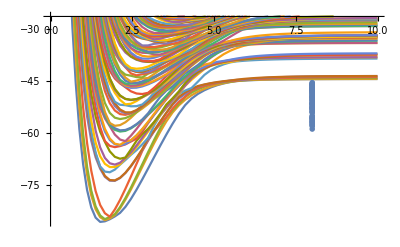

```mathematica
pcurves4=ListPlot[Curves4,Joined->True,PlotRange->{Min[curvestemp4[[2]]],Ecutoff4+18}];
penergies4=ListPlot[Table[{8,eValsBound4[[i]]},{i,1,Length[eValsBound4]}],PlotMarkers->Graphics[{Thickness[.001],Black,Line[{{15,0},{20,0}}]}]];
Show[pcurves4,penergies4]
```

```mathematica
Es4=Table[eValsBound4[[i+1]]-eValsBound4[[i]],{i,1,Length[eValsBound4]-1}];
eTrim4 = Select[Es4,#>0.0000001&];
avg4 = Mean[eTrim4];
eTrim4 = eTrim4/avg4;
Sort[eTrim4];
Length[Es4];
Length[eTrim4];
ρ4=1/avg4;
EspaceBin4=BinCounts[eTrim4,{bins}];
NormBrodyBinCs4=Table[EspaceBin4[[i]]/Total[EspaceBin4]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
brodyPdist4 = Table[{bFit[[i]],NormBrodyBinCs4[[i]]},{i,1,Length[bFit]}]
phist4=ListPlot[brodyPdist4,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Black];
pars4 = FindFit[brodyPdist4,{PBrody[s,w],w>0,w<1},{w},s]
pfit4=Plot[PBrody[s,w/.pars4],{s,0,5},PlotRange->All,PlotStyle->Red];
```

{{0.1,0.2},{0.3,0.4},{0.5,0.8},{0.7,0.666667},{0.9,1.13333},{1.1,0.733333},{1.3,0.266667},{1.5,0.133333},{1.7,0.266667},{1.9,0.2},{2.1,0.0666667},{2.3,0.},{2.5,0.},{2.7,0.},{2.9,0.},{3.1,0.},{3.3,0.},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.0666667},{4.5,0.},{4.7,0.},{4.9,0.0666667}}

{w→0.999995}

```mathematica
pall4=Show[phist4,pfit4,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

-Graphics-

```mathematica
ρ4
```

5.61766

## We need to more closely examine the identical particle symmetries and any other symmetries in the Hamiltonian in order to understand these spectra.

We defined the Jacobi coordinates in the H-tree above so that:

(y⃗)^(12)=S_12 x⃗

where:

1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))

To keep things as general as possible I’ll assume for now that only particle 1 is of different mass and let m_2=m_3=m_4=m, and m_1=γ m  Then

μ_12=(γ m m)/(γ m+m)=mγ/(1+γ) ⟶ m/2

μ_34=m/2

μ_(12,34)=((γ m+m)(2m))/(3m+γ m)=2m(1+γ)/(3+γ)⟶ m

μ=((γ m m m m)/(γ m+3m))^(1/3)=(m(γ/(3+γ)))^(1/3) ⟶ (m/2^(2/3))

So for the equal-mass case:

2^(1/3)/(√m)(√(m/2) | -√(m/2) | 0 | 0
0 | 0 | √(m/2) | -√(m/2)
(√m)/2 | (√m)/2 | -(√m)/2 | -(√m)/2
m/(√(4m)) | m/(√(4m)) | m/(√(4m)) | m/(√(4m)))=2^(1/3)(√(1/2) | -√(1/2) | 0 | 0
0 | 0 | √(1/2) | -√(1/2)
1/2 | 1/2 | -1/2 | -1/2
1/2 | 1/2 | 1/2 | 1/2)

and

x⃗=S_12^-1(y⃗)^(12)

Then

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)

Now note that we could use the same matrix S_12 to construct (y⃗)^(13) if the matrix were to act on a column vector (x_1
x_3
x_2
x_4)  instead of the usual vector x⃗= (x_1
x_2
x_3
x_4).  We can then say:

(x_1
x_3
x_2
x_4) =(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)=P_23 x⃗

Hence:

S_13=S_12 P_23

and

(y⃗)^(13)=S_13 x⃗=S_13 S_12^-1(y⃗)^(12)=S_12 P_23 S_12^-1(y⃗)^(12)

Similarly,

(y⃗)^(14)=S_14 x⃗=S_14 S_12^-1(y⃗)^(12)=S_12 P_24 S_12^-1(y⃗)^(12)

where

P_24=(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
S12=2^(1/3)({{√(1/2), -√(1/2), 0, 0}, {0, 0, √(1/2), -√(1/2)}, {1/2, 1/2, -1/2, -1/2}, {1/2, 1/2, 1/2, 1/2}});
```

```mathematica
P24=({{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}});P23=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});P34=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});P14=({{0, 0, 0, 1}, {0, 1, 0, 0}, {0, 0, 1, 0}, {1, 0, 0, 0}});P13=({{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}});P12=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
```

```mathematica
𝒫12=Simplify[S12.P12.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫12]
```

(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
𝒫34=Simplify[S12.P34.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫34]
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
𝒫14=Simplify[S12.P14.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫14]
```

(1/2 | -1/2 | -1/(√2)
-1/2 | 1/2 | -1/(√2)
-1/(√2) | -1/(√2) | 0)

```mathematica
𝒫13=Simplify[S12.P13.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫13]
```

(1/2 | 1/2 | -1/(√2)
1/2 | 1/2 | 1/(√2)
-1/(√2) | 1/(√2) | 0)

```mathematica
𝒫23=Simplify[S12.P23.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫23]
```

(1/2 | -1/2 | 1/(√2)
-1/2 | 1/2 | 1/(√2)
1/(√2) | 1/(√2) | 0)

```mathematica
𝒫24=Simplify[S12.P24.Inverse[S12]][[1;;3,1;;3]];TraditionalForm[𝒫24]
```

(1/2 | 1/2 | 1/(√2)
1/2 | 1/2 | -1/(√2)
1/(√2) | -1/(√2) | 0)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14]]
```

(0 | -1 | 0
-1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫24.𝒫13]]
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | -1)

```mathematica
TraditionalForm[FullSimplify[𝒫23.𝒫14.𝒫24.𝒫13]]
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

X_cm=(m_1 x_1+m_2 x_2+m_3 x_3+m_4 x_4)/(m_1+m_2+m_3+m_4)

ρ_1^(12)=x_1-x_2

ρ_2^(12)=x_3-x_4

ρ_3^(12)=(m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4)

and mass-scaled Jacobi coordinates as:

y_1^(12)=√(μ_12/μ)(x_1-x_2)

y_2^(12)=√(μ_34/μ)(x_3-x_4)

y_3^(12)=√((μ_(12,34))/μ)((m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4))

y_4^(12)=√(M/μ)X_cm

The convention here is that the superscript (12) indicates this coordinate system is convenient for treating the interaction between particles 1 and 2.  In matrix notation:

(y_1^(12)
y_2^(12)
y_3^(12)
y_4^(12))=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_2
x_3
x_4)

Now we define the hyperspherical coordinates as:

y_1^(12)=cos θ_12

y_2^(12)=sin θ_12 cos ϕ_12

y_3^(12)=sin θ_12 sin ϕ_12

```mathematica
Clear[μ4]
```

```mathematica
μ4=(μ12 μ34 μ1234)^(1/3)/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}
```

((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3)

```mathematica
A=1/(√μ4)({{√μ12, -√μ12, 0, 0}, {0, 0, √μ34, -√μ34}, {(√μ1234 m1)/(m1+m2), (√μ1234 m2)/(m1+m2), -(√μ1234 m3)/(m3+m4), -(√μ1234 m4)/(m3+m4)}, {m1/(√M), m2/(√M), m3/(√M), m4/(√M)}})/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}//FullSimplify
```

{{(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),0,0},{0,0,(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)},{(m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),(m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6))},{m1/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m2/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m3/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m4/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4))}}

Let’s just treat the equal mass case here...

```mathematica
({{x1}, {x2}, {x3}, {x4}})=FullSimplify[Inverse[A].({{x}, {y}, {z}, {XCM}})/.{m1->m,m2->m,m3->β m,m4->β m}];
```

```mathematica
Clear[R]
```

```mathematica
x12=Simplify[x1-x2];FullSimplify[x12,{m>0,β>0}]
x12hyp=Simplify[x12,m>0]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x12hyp,m>0]
```

(2^(1/3) x β^(1/3))/(1+β)^(1/6)

2^(1/3) R (β^2/(1+β))^(1/6) Cos[ϕ] Sin[θ]

```mathematica
x13=FullSimplify[x1-x3,{m>0,β>0}]
x13hyp=Simplify[x13]/.{x->R Sin[θ]Cos[ϕ],y-> R Sin[θ]Sin[ϕ],z-> R Cos[θ]};FullSimplify[x13hyp,{m>0,β>0}]
```

(√m x β-y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]-√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x14=FullSimplify[x1-x4,{m>0,β>0}]
x14hyp=Simplify[x14]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x14hyp,{m>0,β>0}]
```

(√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x23=Simplify[x2-x3,{m>0,β>0}]
x23hyp=Simplify[x23]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x23hyp,{m>0,β>0}]
```

-(√m x β+y √(m β)-z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]-Sin[θ] (√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x24=Simplify[x2-x4,{m>0,β>0}]
x24hyp=Simplify[x24]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x24hyp,{m>0,β>0}]
```

(-√m x β+y √(m β)+z √(m β (1+β)))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

(R (√(m β (1+β)) Cos[θ]+Sin[θ] (-√m β Cos[ϕ]+√(m β) Sin[ϕ])))/(2^(2/3) √m β^(2/3) (1+β)^(1/6))

```mathematica
x34=Simplify[x3-x4,{m>0,β>0}]
x34hyp=Simplify[x3-x4,{m>0,β>0}]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x34hyp,{m>0,β>0}]
```

(2^(1/3) y)/(β (1+β))^(1/6)

(2^(1/3) R Sin[θ] Sin[ϕ])/(β (1+β))^(1/6)

```mathematica
Clear[unequalmassxij]
```

```mathematica
unequalmassxij[R_,β_]=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m->1,θ->t π,ϕ->f π}]
```

{2^(1/3) R (β^2/(1+β))^(1/6) Cos[f π] Sin[π t],(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]-√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]+β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-√β (√β Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(R (√(β (1+β)) Cos[π t]-β Cos[f π] Sin[π t]+√β Sin[f π] Sin[π t]))/(2^(2/3) β^(2/3) (1+β)^(1/6)),(2^(1/3) R Sin[f π] Sin[π t])/((β+β^2)^(1/6))}

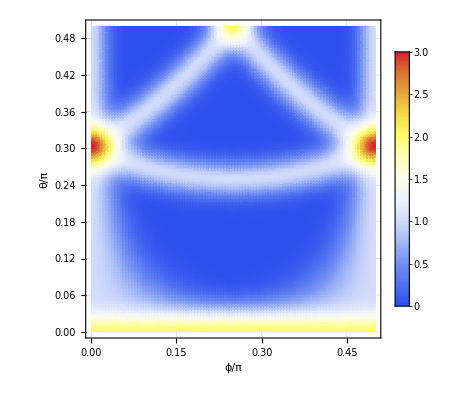

```mathematica
beta=1.0;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2],{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

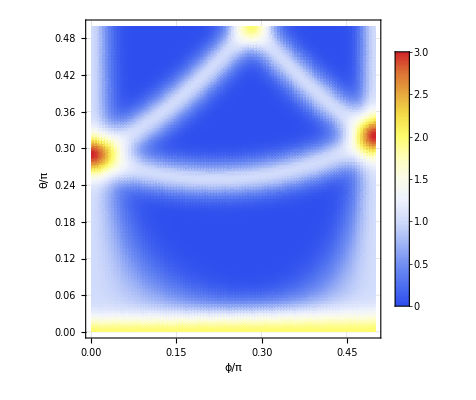

```mathematica
beta=1.5;DensityPlot[Sum[Exp[-(unequalmassxij[10,beta][[i]])^2]/.β->beta,{i,1,6}]==0,{f,0.0,.5},{t,0,0.5},GridLines->Automatic,ColorFunction->"TemperatureMap",FrameLabel->{"ϕ/π","θ/π"},PlotPoints->100,PlotLegends->Automatic]
```

```mathematica
unequalmassxij[[1]]==0
```

Part::partd: Part specification unequalmassxij⟦1⟧ is longer than depth of object.

unequalmassxij⟦1⟧==0

```mathematica
c12[β_]:=ContourPlot[Evaluate[unequalmassxij[[1]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Black,FrameLabel->{"ϕ/π","θ/π"}]
c13[β_]:=ContourPlot[Evaluate[unequalmassxij[[2]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Red,FrameLabel->{"ϕ/π","θ/π"}];
c14[β_]:=ContourPlot[Evaluate[unequalmassxij[[3]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Blue,FrameLabel->{"ϕ/π","θ/π"}];
c23[β_]:=ContourPlot[Evaluate[unequalmassxij[[4]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Green,FrameLabel->{"ϕ/π","θ/π"}];
c24[β_]:=ContourPlot[Evaluate[unequalmassxij[[5]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Orange,FrameLabel->{"ϕ/π","θ/π"}];
c34[β_]:=ContourPlot[Evaluate[unequalmassxij[[6]]==0],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Yellow,FrameLabel->{"ϕ/π","θ/π"}];
```

```mathematica
c12[1.0]
```

Part::partd: Part specification unequalmassxij⟦1⟧ is longer than depth of object.

-Graphics-

Show::gcomb: Could not combine the graphics objects in Show[{c12,c13,c14,c23,c24,c34},].

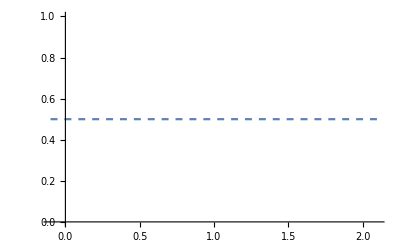
Show[{c12,c13,c14,c23,c24,c34},-Graphics-]

```mathematica
pall=Show[{c12,c13,c14,c23,c24,c34},Plot[0.5,{x,-.1,2.1},PlotStyle->Dashed]]
```

```mathematica
cptable=Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,0,.5},{t,0,.5},GridLines->Automatic,ContourStyle->Black],{i,1,6}];
```

Part::partd: Part specification unequalmassxij⟦1⟧ is longer than depth of object.

Part::partd: Part specification unequalmassxij⟦2⟧ is longer than depth of object.

Part::partd: Part specification unequalmassxij⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Show[pall,PlotRange->{{0,0.5},{0,0.5}}]
```

Show::gtype: Show is not a type of graphics.

Show[Show[{c12,c13,c14,c23,c24,c34},-Graphics-],PlotRange→{{0,0.5},{0,0.5}}]

### Construct a simpler model with numerical solution

Consider a 3D Hamiltonian of the form

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

H=ℏ^2/(2μ)∇^2 + 1/2μ r^2+k_xy x y+k_xz x z+k_yz y z

Sakurai, Modern QM page 217 (translated to my preferred notation)

∫ⅆΩ Y_l^(m*)(Ω)Y_l_1^m_1(Ω)Y_l_2^m_2(Ω)=√(((2 l_1+1)(2 l_2+1))/(4π (2l+1)))l_1 0, l_2 0(l_1 l_2) l 0l_1 m_1 l_2 m_2 (l_1 l_2) l m

```mathematica
ME3[l_,m_,l1_,m1_,l2_,m2_]:=√(((2l1+1)(2l2+1))/(4π (2l+1)))ClebschGordan[{l1,0},{l2,0},{l,0}]ClebschGordan[{l1,m1},{l2,m2},{l,m}]
```

So if we need matrix elements of the form:

∫ⅆΩ Y_l^(m*)(Ω)Y_2^m_1(Ω)Y_l_2^m_2(Ω)=√((5(2 l_2+1))/(4π (2l+1)))2,0, l_2,0(l_1 l_2) l 02 m_1 l_2 m_2 (2 l_2) l m

```mathematica
Simplify[ME3[l,m,2,m1,l2,m2]]
```

Piecewise[{{1/(2 (2+l-l2) (l-l2)!)(-1)^(-3 l2+m) (1+2 l) (l^3+l^2 (1+l2)-l (2+2 l2+l2^2)-l2 (2+3 l2+l2^2)) √((5+10 l2)/(π+2 l π)) √(((2+l-l2)!)/((-1+l+l2) (l+l2) (1+l+l2) (2+l+l2) (3+l+l2) (2-l+l2)!)) ThreeJSymbol[{2,m1},{l2,m2},{l,-m}], l∈ℤ&&l2∈ℤ&&l≥0&&l2≥0&&l+l2≥2&&l2≤2+l&&l≤2+l2}, {0, True}}]

Now, since we know

x y = r^2 √(30/π)i (Y_2^-2-Y_2^2)

```mathematica
MExy[R_,l_,m_,l2_,m2_]:=R^2 ⅈ √(30/π)(ME3[l,m,2,-2,l2,m2]-ME3[l,m,2,2,l2,m2])
```

Now the issue is if we want to apply this model to test the two-component 4-fermion problem in 1D, then we need to know how to construct systematically the symmetrized 4-fermion harmonics.  We can specify the subset of harmonics by the boundary conditions implied by identical particle symmetry:

ψ(ϕ=0,θ)=ψ(ϕ=π/2,θ)=0

requires a superposition ψ~Y_l^m-(-1)^m Y_l^-m

```mathematica
Integrate[SphericalHarmonicY[lb,mb,θ,ϕ]SphericalHarmonicY[k,q,θ,ϕ]SphericalHarmonicY[lk,mk,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

$Aborted